# Axial Shimming

## Last Updated: 2025/11/08

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Evaluations

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

```mathematica
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

# Old Data

Dataset Structure: {
	{ion_pos_x,ion_pos_y}, {volt_east_endcap, volt_west_endcap},
	{carrier_rabi_freq_val_wkhz, carrier_rabi_freq_err_wkhz},
	{xum_bsb_rabi_freq_val_wkhz, xum_bsb_rabi_freq_err_wkhz}
}

## 2025/08

```mathematica
(*2025/08/09: during EGGS field gradient investigation*)
(*todo: get errors*)
dataDJ20250809={
{{238,335},{182,343},{1./13.43}},
{{255,335},{190,330},{1./24.39}},
{{282,337},{205,308},{1./14.84}},
{{283,336},{205,308},{1./22.50}},
{{306,337},{217,290},{1./10.90}},
{{319,338},{224,282},{1./13.17}},
{{330,337},{231,275},{1./8.18}},
{{351,339},{243,261},{1./5.05}},
{{362,339},{250,254},{1./4.96}},
{{383,340},{263,242},{1./3.95}}
};
```

## 2025/10

```mathematica
(*2025/10/18: beginning of CASR Fock Campaign 2*)
dataDJ={
{{198,338},{174,357},{230.,0.9},{10.9,0.03}},
{{206,337},{178,350},{216.,3.},{1.57,0.09}},
{{210,337},{180,346},{226.,0.9},{3.04,0.01}},
{{214,338},{182,343},{171.,2.},{1.46,2}},
{{230,338},{190,331},{222.,1.},{8.76,0.05}},
{{246,339},{198,319},{233.,2.},{20.6,0.04}}
};
```

```mathematica
(*2025/10/28: cooldown after the accidental lakeshore "bakeout"*)
dataDJ={
{{176,310},{174,360},{234.,0.8},{10.9,0.03}},
{{184,310},{177,353},{244.,1.},{2.53,0.1}},
{{192,310},{181,347},{240.,1.},{4.68,0.3}},
{{192,310},{181,347},{240.,1.},{4.68,0.3}},
{{200,311},{185,340},{242.,0.3},{8.57,0.05}}
(*{{230,338},{190,331},{222.,1.},{8.76,0.05}},
{{246,339},{198,319},{233.,2.},{20.6,0.04}}*)
};
```

## 2025/11

```mathematica
(*2025/11/08: preparing for CASR round 2*)
dataDJ={
{{184,311},{177,353},{235,0.9},{2.7,2.}},
{{192,310},{181,347},{224.,0.7},{12.8,0.04}}
};
```

# Process!

Select Target Data for Processing

```mathematica
(*2025/11/08: preparing for CASR round 2*)
dataDJ={
{{184,311},{177,353},{235,0.9},{2.7,2.}},
{{192,310},{181,347},{224.,0.7},{12.8,0.04}}
};
```

## Process All

## Process Data

```mathematica
(*sort data by x-axis target*)
dataProcessDJ=Sort[dataDJ,#1[[1,1]]<#2[[1,1]]&];
```

```mathematica
(*extract x-axis data*)
xAxisData=dataProcessDJ[[;;,1,1]];
```

```mathematica
(*replace 0 uncertainties with some minimum value then convert to Around*)
dataProcessDJ[[;;,3,2]]=dataProcessDJ[[;;,3,2]]/.{(0|0.)->0.001};
dataProcessDJ[[;;,4,2]]=dataProcessDJ[[;;,4,2]]/.{(0|0.)->0.001};
```

```mathematica
(*convert rabi freqs to Around to simplify error propagation, then calculate rabi ratio*)
rabiRatioData=(Around@@@#)&/@{dataProcessDJ[[;;,4]],dataProcessDJ[[;;,3]]};
rabiRatioData=Divide@@rabiRatioData;
```

```mathematica
(*create dataset for plotting*)
dataXUMNull=Transpose[{
xAxisData,
rabiRatioData
}];
```

## Prepare Fit Function

```mathematica
(*create abs fit func for general use*)
FitAbsFunc[data_,fitWeights_:None]:=Block[{Ampl,x,x0,C0},
With[
{
fitfunc=Ampl*Abs[x-x0]+C0,
fitConstraintsDJ={Ampl>0.,C0>0.},
fitGuessDJ={
{Ampl,Abs[(Subtract@@#[[;;,2]])/(Subtract@@#[[;;,1]])]&[data[[First/@{Ordering[data[[;;,2]],-1],Ordering[data[[;;,2]],1]}]]]},
{x0,First@data[[Ordering[data[[;;,2]],1],1]]},
{C0,Min[data[[;;,2]]]}
}
},

Return[NonlinearModelFit[data,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
x,

Weights->fitWeights
]
];
]];
```

## Do Fits

```mathematica
(*separate values from uncertainties*)
dataFitValues=Transpose[{dataXUMNull[[;;,1]],#["Value"]&/@dataXUMNull[[;;,2]]}];
dataFitWeights=(#["Uncertainty"]&/@dataXUMNull[[;;,2]])^-2.;
```

```mathematica
(*fit xum field null to abs func*)
AbsoluteTiming[
fitXUMNull=FitAbsFunc[dataFitValues,dataFitWeights];
]
```

{0.0072579,Null}

```mathematica
(*get fit params*)
fitXUMParams=Style[
fitXUMNull["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

### Plot Raw Data

```mathematica
(*plot trap xum null data*)
summaryXUMFigure=Show[{
ListPlot[
{dataXUMNull,dataXUMNull},
PlotRange->{
{Full,Full},
{0.,Full}
},

FrameLabel->{ 
{Style["Micromotion Index (β)",{Black,Directive[15]}],None},
{
Style["Ion Position (pixels)",{Black,Directive[15]}],
Style["Trap RF Field Null (Axial)",{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[2]],PointSize[0.018]},
{DefaultPlotColors[[2]],Dashed,Thickness[0.0027]}
},
Joined->{
False,True,
False,True,
False,True
},
PlotLegends->{
"XUM Null",None
},

ImageSize->Scaled[0.51]
],

(*combine with fitted plot*)
fitXUMPlot
}];
```

### Plot Fit

```mathematica
(*plot fitted results*)
fitXUMPlot=Plot[
fitXUMNull[x],
{x,Min[dataXUMNull[[;;,1]]],Max[dataXUMNull[[;;,1]]]},
PlotStyle->{DefaultPlotColors[[2]],Thickness[0.0033],Opacity[0.85]}
];
```

## Show

| Estimate | Standard Error | Confidence Interval
Ampl | 0.00340086 | 0.00084759 | {-0.00024603,0.00704774}
x0 | 189.278 | 0.690882 | {186.305,192.25}
C0 | -9.5682×10^-9 | 0.00959203 | {-0.0412712,0.0412712}

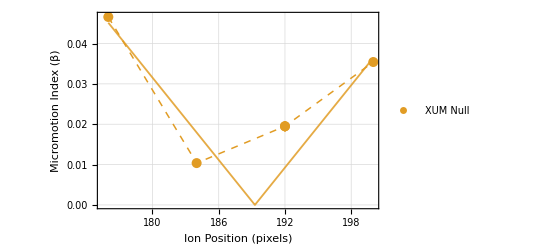

```mathematica
fitXUMParams
summaryXUMFigure
```